Coded by Manish J. Thapa for Advanced Kinetics class at ETH Zurich, Switzerland

```mathematica
Needs["Notation`"];(*useful when one wants to write subscripts and superscripts*)
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

## Square Barrier

```mathematica
ClearAll;
```

```mathematica
Clear[Subscript[k, 1],Subscript[k, 2],m,a,Subscript[V, 0],t,r];
```

```mathematica
param={Subscript[k, 1]->√(2m Subscript[E, n]),Subscript[k, 2]->√(2m (Subscript[E, n]-Subscript[V, 0])),Subscript[V, 0]->1,a->1};(**do not use E as the variable, mathematica thinks of it as an exponential*)
```

```mathematica
(*V0 is the barrier height, and a is the width, k1 and k2 are the momentum of the particle*)
```

## Solution

```mathematica
(*We have 3 kinds of wave functions**)
```

```mathematica
Subscript[ψ, 1]=Exp[I Subscript[k, 1] x]+ r Exp[-I Subscript[k, 1] x];
```

```mathematica
Subscript[ψ, 2]=A Exp[I Subscript[k, 1] x]+ B Exp[-I Subscript[k, 2] x];(*interaction*)
```

```mathematica
Subscript[ψ, 3]=t Exp[I Subscript[k, 1] x];
```

```mathematica
(******solving equations satisfying boundary conditions; using continuity of the wavefunctions and their derivatives at the interface gives*******)
```

```mathematica
Subscript[f, 1]=A+B-r-1;(*conservation of flux*)
```

```mathematica
Subscript[f, 2]=A Exp[I Subscript[k, 2] a]+B Exp[-I Subscript[k, 2] a]-t Exp[I Subscript[k, 1] a];
```

```mathematica
Subscript[f, 3]=Subscript[k, 1](1-r)-Subscript[k, 2](A-B);
```

```mathematica
Subscript[f, 4]=Subscript[k, 2](A Exp[I Subscript[k, 2] a]-B Exp[-I Subscript[k, 2] a])-Subscript[k, 1] t Exp[I Subscript[k, 1] a];
```

```mathematica
(**t is transmission probbaility amplitude, whereas r is reflection probability amplitude**)
```

```mathematica
sol=Solve[{Subscript[f, 1]==0,Subscript[f, 2]==0,Subscript[f, 3]==0,Subscript[f, 4]==0},{A,B,r,t}]
```

{{A→-(2 k_1 (k_1+k_2))/(-k_1^2+ⅇ^(2 ⅈ a k_2) k_1^2-2 k_1 k_2-2 ⅇ^(2 ⅈ a k_2) k_1 k_2-k_2^2+ⅇ^(2 ⅈ a k_2) k_2^2),B→(2 ⅇ^(2 ⅈ a k_2) k_1 (k_1-k_2))/(-k_1^2+ⅇ^(2 ⅈ a k_2) k_1^2-2 k_1 k_2-2 ⅇ^(2 ⅈ a k_2) k_1 k_2-k_2^2+ⅇ^(2 ⅈ a k_2) k_2^2),r→((-1+ⅇ^(2 ⅈ a k_2)) (k_1-k_2) (k_1+k_2))/(-k_1^2+ⅇ^(2 ⅈ a k_2) k_1^2-2 k_1 k_2-2 ⅇ^(2 ⅈ a k_2) k_1 k_2-k_2^2+ⅇ^(2 ⅈ a k_2) k_2^2),t→-(4 ⅇ^(-ⅈ a k_1+ⅈ a k_2) k_1 k_2)/(-k_1^2+ⅇ^(2 ⅈ a k_2) k_1^2-2 k_1 k_2-2 ⅇ^(2 ⅈ a k_2) k_1 k_2-k_2^2+ⅇ^(2 ⅈ a k_2) k_2^2)}}

```mathematica
t=t//.sol[[1,4]]//FullSimplify
```

(2 ⅈ ⅇ^(-ⅈ a k_1) k_1 k_2)/(2 ⅈ k_1 k_2 Cos[a k_2]+(k_1^2+k_2^2) Sin[a k_2])

```mathematica
T=Abs[t]^2//.param//FullSimplify (*transmission probability*)
```

16 ⅇ^(2 √2 Im[√(E_n m)]) Abs[((-1+E_n) E_n m^2)/(4 ⅈ √((-1+E_n) m) √(E_n m) Cos[√2 √((-1+E_n) m)]+2 (-1+2 E_n) m Sin[√2 √((-1+E_n) m)])^2]

```mathematica
r=r//.sol[[1,3]]//FullSimplify
```

((k_1-k_2) (k_1+k_2) Sin[a k_2])/(2 ⅈ k_1 k_2 Cos[a k_2]+(k_1^2+k_2^2) Sin[a k_2])

```mathematica
R=Abs[r]^2//.param(*reflection probability*)
```

Abs[((-√2 √((-1+E_n) m)+√2 √(E_n m)) (√2 √((-1+E_n) m)+√2 √(E_n m)) Sin[√2 √((-1+E_n) m)])/(4 ⅈ √((-1+E_n) m) √(E_n m) Cos[√2 √((-1+E_n) m)]+(2 (-1+E_n) m+2 E_n m) Sin[√2 √((-1+E_n) m)])]^2

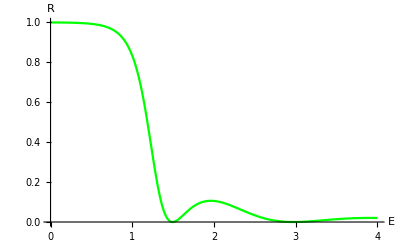

```mathematica
p1=Plot[R//.param//.{m->10},{Subscript[E, n],0,4},AxesLabel->{"E","R"},PlotStyle->Green]
```

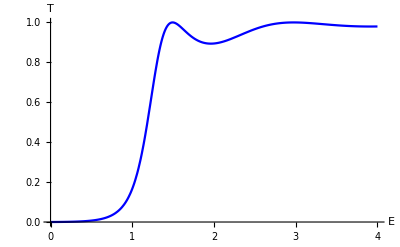

```mathematica
p2=Plot[T//.param//.{m->10},{Subscript[E, n],0,4},AxesLabel->{"E","T"},PlotStyle->Blue]
```

```mathematica
(*destructive interfereces are observed between transmitted and reflected waves hence the beats*)
```

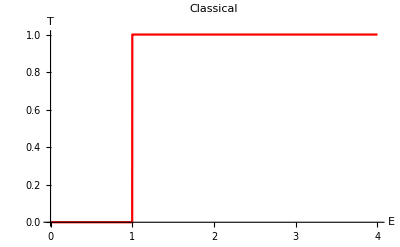

```mathematica
p3=Plot[Piecewise[{{1,E>Subscript[V, 0]},{0,E<Subscript[V, 0]}}]//.param,{E,0,4},PlotStyle->Red,AxesLabel->{"E","T"},PlotLabel->"Classical"]
```

```mathematica
(*this is illustration, one can also see this (no tunneling) in the limit when m is very large, checkout the manipulate plot below*)
```

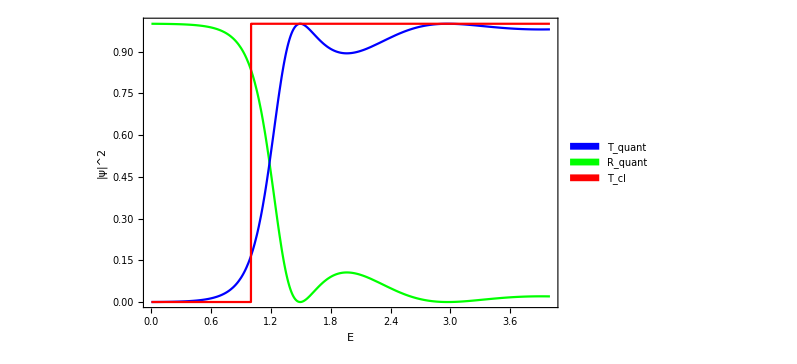

```mathematica
Legended[Show[p1,p2,p3,AxesStyle->Black,FrameLabel->{"E","|ψ|^2"},Frame->True,FrameTicks->All,ImageSize->590,PlotRange->All,BaseStyle->{12,FontFamily->"Helvetica"}],Placed[SwatchLegend[{Blue,Green,Red},{Style["T_quant",12],Style["R_quant",12],Style["T_cl",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.7,0.1},{0,0}}]]
```

```mathematica
p4=Manipulate[Plot[T//.param//.{m->M},{Subscript[E, n],0,4},AxesLabel->{"E","T"}],{M,1,100}](**transmission probability**)
```

```mathematica
(*what happens when M>>1? change the barrier height and width in the param to see the difference*)
```